# Math2200: Applied Mathematics

## 2009 Semester 1 — Final Exam

Student ID = type it here                                                                                 Total Mark = mark

## Section. Instructions:

Time allowed : 3 hours

TYPE YOUR STUDENT NUMBER IN THE BOX PROVIDED

Save your notebook now and save regularly during the test.
Save either on the network server in the MCL or to a memory stick, in case your computer crashes.

This is an “open-book” exam. You are permitted to bring in printed or electronic copies of your lecture notes and assignment solutions, and to access electronic resources such as the Documentation Center and the internet.

Spoken or electronic communication via email, messaging, chat, file transfer, etc. is not permitted. Such action may result in your being deprived of any credit for this examination or even, in some cases, for the whole unit. This will apply regardless of whether the material has been used at the time it is found.

Insert your solutions—both Mathematica code and text—directly into the Notebook below the Solution cell that immediately follows the part of the question that you are answering.

When asked to do so by the examination supervisor, upload your solutions using the file name student#.nb to the Exam folder on the Physics FTP server.  (Follow normal path from the desktop with "student" username.)
Stay seated and do not talk until the examination supervisors verify that the correct number of notebooks have been uploaded.

## Section. Mathematica calculations and programming. [20 Marks]

Question SectionExercise)   [4 Marks]

One of the most important steps in using Mathematica is translating a given problem into useful Mathematica code.   Our first, example comes from Chemistry.

The first step in the production of chromium metal from the chromite ore, Fe Cr_2 O_4 is the following reaction.

Fe Cr_2 O_4 + Na_2 CO_3+O_2 ⟶^(+ heat) Na_2Cr O_4+Fe_2 O_3+CO_2

In this reaction the iron is oxidised from its 2+ form to its 3+ form, the carbonate decomposes to carbon dioxide and the dichromate ion is changed to a chromate ion.  The above is not a balanced reaction.   Use Mathematica to find the smallest positive integers x_1,…,x_6 such that all atomic species in

x_1 Fe Cr_2 O_4 + x_2 Na_2 CO_3+x_3 O_2 ⟶^(+ heat) x_4 Na_2 Cr O_4+x_5 Fe_2 O_3+x_6 CO_2

are balanced.  The last line in your code should output the list of integers {x_1,x_2,x_3,x_4,x_5,x_6}.   [4 Marks]

Hint/Clarification:  There are six unkown coefficients and five atomic species above: Iron—Fe, Chromium—Cr, Oxygen—O, Sodium—Na and Carbon—C.
If you need some more clarifaction or examples, look here:  http://en.wikipedia.org/wiki/Chemical_equation.

Solution:

Question SectionExercise)   [4 Marks]

Pattern matching is the core of most of Mathematica's functionality.  It is also a very powerful tool in a wide range of areas, as anyone who has used Regular Expressions would know.  In fact, the below exercise could be done with regular expressions or String Patterns.

Here are the first four sentences from the Grimm brothers ‘Rapunzel’, freely available from Project Guteneurg.

```mathematica
rapunzel="There were once a man and a woman who had long in vain wished for a child. At length the woman hoped that God was about to grant her desire. These people had a little window at the back of their house from which a splendid garden could be seen, which was full of the most beautiful flowers and herbs. It was, however, surrounded by a high wall, and no one dared to go into it because it belonged to an enchantress, who had great power and was dreaded by all the world.";
```

We can turn it into a list of single characters and remove non alphabetic characters using:

```mathematica
rapunzelList=Select[Characters[ToLowerCase[rapunzel]],MemberQ[CharacterRange["a","z"],#]&]
```

{t,h,e,r,e,w,e,r,e,o,n,c,e,a,m,a,n,a,n,d,a,w,o,m,a,n,w,h,o,h,a,d,l,o,n,g,i,n,v,a,i,n,w,i,s,h,e,d,f,o,r,a,c,h,i,l,d,a,t,l,e,n,g,t,h,t,h,e,w,o,m,a,n,h,o,p,e,d,t,h,a,t,g,o,d,w,a,s,a,b,o,u,t,t,o,g,r,a,n,t,h,e,r,d,e,s,i,r,e,t,h,e,s,e,p,e,o,p,l,e,h,a,d,a,l,i,t,t,l,e,w,i,n,d,o,w,a,t,t,h,e,b,a,c,k,o,f,t,h,e,i,r,h,o,u,s,e,f,r,o,m,w,h,i,c,h,a,s,p,l,e,n,d,i,d,g,a,r,d,e,n,c,o,u,l,d,b,e,s,e,e,n,w,h,i,c,h,w,a,s,f,u,l,l,o,f,t,h,e,m,o,s,t,b,e,a,u,t,i,f,u,l,f,l,o,w,e,r,s,a,n,d,h,e,r,b,s,i,t,w,a,s,h,o,w,e,v,e,r,s,u,r,r,o,u,n,d,e,d,b,y,a,h,i,g,h,w,a,l,l,a,n,d,n,o,o,n,e,d,a,r,e,d,t,o,g,o,i,n,t,o,i,t,b,e,c,a,u,s,e,i,t,b,e,l,o,n,g,e,d,t,o,a,n,e,n,c,h,a,n,t,r,e,s,s,w,h,o,h,a,d,g,r,e,a,t,p,o,w,e,r,a,n,d,w,a,s,d,r,e,a,d,e,d,b,y,a,l,l,t,h,e,w,o,r,l,d}

Your task is to find all palindromic sublists of length greater than 2.  (Note: the palindromes do not have to form real words.)  
Your replacement rules should return the palindrome and its starting position in the list.
For example, the first and the last palindrome in the list above are:
{"e", "r", "e"}  starting in the 3^rd position and {"d", "e", "d"} starting in the 352^nd position. [4 Marks]

Solution:

Question SectionExercise)   [12 Marks]

One of the first and most useful formula you would have learnt in high-school algebra is the solution of a quadratic:

x^2+bx+c==0   ⟹   x=x_±=(-b±√(b^2-4c))/2

A result that is trivially reproduced and checked with Mathematica:

```mathematica
Reduce[x^2+b x+c==0,x]
```

x==1/2 (-b-√(b^2-4 c))||x==1/2 (-b+√(b^2-4 c))

We can think of this operation as a map, f, that takes two complex numbers, a and b, and returns the pair of complex numbers x_+ and x_-.  When we define this map, we have a choice of ordering to make: should it return (x_+,x_-) or (x_-,x_+)?  We'll define a map for each choice:

f_±:ℂ^2→ℂ^2 ,                         f_±:(b,c)↦((-b±√(b^2-4c))/2,(-b∓√(b^2-4c))/2)

Some examples  f_+(0,1)=(ⅈ,-ⅈ),  f_-(0,1)=(-ⅈ,ⅈ),  f_+(3,-4)=(1,-4), etc…

Now, in general, if we have a map that takes one object in a set to another in the set (in our case the objects are pairs of complex numbers) then we can iterate the map:

f:𝒮→𝒮:a↦f(a)
 f^(n)(a)=f(f^(n-1)(a))=… =f(f(f⋯f(a)))

If there exists an element p∈𝒮 such that f(p)=p, then p is called a fixed point of the map f.
If there exists an element q∈𝒮 and an integer ν>0 such that f^(ν)(q)=q then it must be that the sequence (q,f(q),… f^(ν-1)(q)) is repeated forever.  This is called a orbit or cycle of f with period ν.  An orbit with period 1 is a fixed point.

In the case of our maps f_± there is always the trivial fixed point f_±(0,0)=(0,0).  
Below, we will aslo investigate some other fixed points and orbits of our maps.  
It is also possible to investigate the behaviour of repeatedly applying various sequences of maps, such as a↦f_+(f_-(a)) etc…  
The existence and stability of the orbits of these more complicated maps is an open question.  
It can be shown that any combination of the maps f_± yield bounded sequences, 
the bound is illustrated in the picture on the right, that you will reproduce in part iv.3).  | -Graphics-

Define a function f({b,c},ord) that returns {x_+,x_-} if ord=1,   {x_-,x_+} if ord=-1 or a RandomChoice of {x_±,x_∓} if ord=0.
Test it by reproducing the examples given above:  ie on  {f[{0,1},1],f[{0,1},-1],f[{3,-4},1]}   [2 Marks]

Prove/show that f_+ has two fixed points (including the above trivial one) whilst f_- has only the trivial fixed point.   [2 Marks]

1) Define a function that takes a list of pairs of complex numbers, such as that created by using NestList with one of our functions, and outputs a 2D graphics of the complex numbers as points on the Argand (complex) plane.  Make the first number in each pair a red point and the second number a blue point.
2) Test it on  NestList[Times[{ⅇ^(π ⅈ/25),ⅇ^(-π ⅈ/25)},#]&,{1,1},25].  Is the output what you expected?   [2 Marks]

In the following, use randomised initial points generated by {b_0,c_0}=RandomComplex[(1+ⅈ){-1,1},2].
1) Use the above graphics function to plot all of the points created by 10^3 iterations of f_+ starting at {b_0,c_0}.
2) Similarly plot the action of f_- on {b_0,c_0}.
3) Now plot the action of f_0 (ie repeatedly random choices of f_+ or f_-) on {b_0,c_0}.
	 — You should get a picture like the one given above.   [2 Marks]

Hint:  You might need to use some pure function notation to do the above nested actions.

Hint:  If you want a cleaner plot for part 2) try omitting the first 50 or so points from the plot.

The graphs from 1) and 2) of the above should confirm your results from part ii.   ie f_+ converges to a fixed point and f_- doesn't converge to a fixed point,  but it does converge to a finite number of points, ie an orbit.
Extract the last 24 complex pairs from the list that generated the above graphics for f_- and use them to guess the period of the orbit of f_-?   [2 Marks]

Hint:  You can extract the last n elements of a list using Part — eg, ThisIsAList⟦-n;;⟧.

Finding cycles is not always straight forward, and we don't always have to guide the process by hand.  Thus we can automate the process using one of various algorithms.  The one that we'll implement here is called Floyd's algorithm, or the “tortoise and hare” algorithm.

The algorithm takes a map (f) and a initial “point” (x) as input and returns the number of steps where the cycle first starts (μ) and the length of the cycle (λ)  (optionally, it can also return the values during the cycle (f^(μ)(x),f^(μ+1)(x),…,f^(μ+λ)(x)) ).

The algorithm has three phases:

①  —  Find an instance where f^(n)(x)=f^(m)(x)  —
Let tortoise=x, hare=f(x)
   while  tortoise≠hare 
      tortoise=f(tortoise), hare=f(f(hare))

②  —  Find the first such value  —
Let hare=tortoise, tortoise=x,  μ=0  
   while  tortoise≠hare 
      tortoise=f(tortoise), μ=μ+1￿

③ —  Find the minimum cycle length  —
Let hare=f(tortoise),  λ=0  
   while  tortoise≠hare 
      hare=f(hare), λ=λ+1

Implement this algorithm and check that it finds the correct fixed point for f_+ and cycle for f_-.  
The map (a,b)↦f_-(f_+(f_+(a,b))) also converges to a cycle, what is its period?		  [2 Marks]

Solution

## Section. Evolving polygon [20 Marks]

There are many examples in physics and engineering where the dynamics of some system is influenced by, even defined by, its geometry.

The geometric property of curvature is, for some systems, a factor in determining how the system evolves.
Real examples include (i) anything with surface tension effects and (ii) general relativity.

The example which follows has been selected not because of any applications but because it can use the methods treated in MATH2200.

The dynamics we're interested in is based on a cyclic matrix: the first part of this question is about this matrix.

Here is some code that will generate such a matrix given a vector,

```mathematica
CyclicMatrix[v_List]:=NestList[RotateRight,v,Length[v]-1]
```

Let's define the cyclic matrix A(n) by

```mathematica
A[n_Integer?(#>2&)]:=CyclicMatrix[RotateLeft[PadRight[{-1,2,-1},n],1]]
```

```mathematica
MatrixForm/@(A/@Range[3,7,2])
```

{(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2),(2 | -1 | 0 | 0 | -1
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
-1 | 0 | 0 | -1 | 2),(2 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 2 | -1 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1
-1 | 0 | 0 | 0 | 0 | -1 | 2)}

Question SectionExercise)  [4 Marks]

Show that, for general integer n>2, the nullspace of A(n) is non-trivial.

Using Mathematica show that, for each of n=4, n=5 and n=6, the nullspace of A(n) is one-dimensional.

Write some text which establishes that, for general positive integer n, the nullspace of A(n) is one-dimensional.

Solution

Consider a list of n points in the complex plane, {z_1,z_2,…,z_n}.  By cyclicly joining the points we construct an n-sided polygon.
Specify an inward pointing direction at a vertex z_j to be

N_j==(z_(j+1)-z_j)-(z_j-z_(j-1))

where the indices j are cyclic (ie j+n=j).

Now consider the vertices as functions of time, z_j=z_j(t), which evolve in the directions N_j:

(ⅆ z_j)/ⅆt==N_j==(z_(j+1)-z_j)-(z_j-z_(j-1))

By writing z⃗==(z_1,z_2,…,z_n)ᵀ and using A(n) is as above, we can write this as the matrix equation

(ⅆ z⃗)/ⅆt+A(n)·z⃗==0 .

What can be shown is that pretty well any randomly chosen initial polygon evolves towards an ‘affinely regular polygon’, e.g. any randomly chosen initial quadrilateral evolves towards a parallelogram.

By summing the equations we can see that the vertex sum, ∑z_j, stays constant.  So without loss of generality, we can take the initial vertices so to be centered around zero.

Here is some code that you can use to plot any polygon given as a list of complex numbers.

```mathematica
showNgon[lst_]:=ListPlot[{Re[#],Im[#]}&/@Append[lst,First@lst],
PlotStyle->PointSize[Large],Joined->True,Mesh->All,AxesOrigin->{0,0},PlotRange->1.1Max[Abs/@lst]{{-1,1},{-1,1}}]
```

Let's plot a random quadrilateral:  (it might be a crossed quadrilateral, but that is not important)

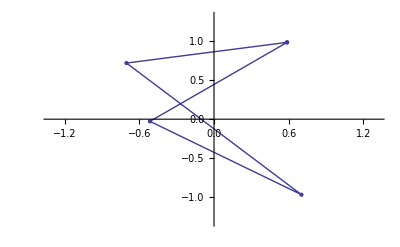

```mathematica
showNgon[RandomComplex[{-1-ⅈ,1+ⅈ},4]]
```

To make a quadrilateral centered at (0,0) we can use the vertices (#1-Mean[#1]&)[RandomComplex[{-1-ⅈ,1+ⅈ},4]].

Question SectionExercise)  [4 Marks]

Have Mathematica find the eigenvalues and eigenvectors of A(4) and find the matrix exponential of (-t A(4)).

Use a Mathematica manipulate command to plot the evolution in time of an initally random quadrilateral under the above system DEs.

Solution

The shapes, at large time are in general ‘affinely regular polygons’.  When n=4, these are parallelograms. Continuing with our normalisation convention of ∑z_i=0, a parallelogram is defined by two vertices z_1 and z_2 with the 3^rd and 4^th vertices are -z_1 and -z_2 respectively.

After a time t, our intial parallelogram has evolved to z⃗(t)=ⅇ^(-t A)·(z_1,z_2,-z_1,-z_2)ᵀ

Question SectionExercise)  [3 Marks]

Show that under the DE (DisplayFormulaNumbered), parallelograms evolve as parallelograms.

Solution

Given the n points in the plane, z⃗=(z_1,z_2,…,z_n)ᵀ, there is (up to multiplication by a constant) a unique n-th degree polynomial with these points as its zeros.

p_(z⃗)(w)==(w-z_1)⋯(w-z_n) .

Question SectionExercise)  [3 Marks]

Given the polynomial from a parallelogram,

```mathematica
Subscript[pp, {z1_,z2_}][w_]:=(w-z1)(w-z2)(w+z1)(w+z2)
```

show that the zeros of its derivative (with respect to w) lie on a straight line.

Solution

Question SectionExercise)  [3 Marks]

As in Exercise 2b, use a Mathematica Manipulate command to plot the evolution in time t , according to our system of d.e.s, of the quadrilateral formed by the evolution a random quadrilateral, shown in blue.
Within the manipulate also show, in red, the zeros of the derivative of the polynomial whose zeros are the vertices of the evolving quadrilateral.

(Remark. You should see the 3 red points evolving towards a straight line.)

Solution

Question SectionExercise)  [3 Marks]

As in Question 2e), use a Mathematica Manipulate command to plot the evolution in time t , according to our system of d.e.s, of the hexagon formed by the evolution a random initial hexagon, shown in blue.
Within the manipulate also show, in red, the zeros of the derivative of the polynomial whose zeros are the vertices of the evolving hexagon.

(Remark. You should see the 5 red points evolving towards a straight line.)

Solution

## Section. Nonlinear oscillations [20 Marks]

#### The Poincaré-Lindstedt formulæ

Suppose that f is an analytic function with f(r_eq)==0.  Consider the differential equation,

r''+f(r)==0,   where  r=r(t)

a first integral of which is E is constant where

E(r,r')==1/2(r')^2+F(r)    with  F(r)==∫f(r)ⅆa.

Approximate, setting f'(r_eq)==ν_0^2,

f(r)==ν_0^2 (r-r_eq)+1/2 f''(r_eq)(r-r_eq)^2+1/6 f'''(r_eq)(r-r_eq)^3+…

Then, as found by a Poincaré-Lindstedt asymptotic approximation, the small oscillations about equilibrium satisfy, when ϵ tends to zero,

r(t)≃r_eq+ϵ cos(νt)+ϵ^2/(4 ν_0^2)f''(r_eq) (1/3 cos(2νt)-1)+…≡r_eq+ϵ cos(νt)+ϵ^2 (1/3 cos(2νt)-1)r_2+…
ν≃ν_0 (1+(9 (f'''(r_eq)/6)ν_0^2-10 (f''(r_eq)/2)^2)/(24 ν_0^4)ϵ^2+…)≡ν_0+ϵ^2 ν_2+…

Question SectionExercise)  [3 Marks]

Write a function that implements the Poincaré-Lindstedt formulæ, (DisplayFormulaNumbered).  That is, given a function f with an equilibrim point r_eq satisfying f(r_eq)==0, your function should return the coeffecients ν_0, ν_2 and r_2.

Solution:

Question SectionExercise)  [2 Marks]

Consider the DE  r''(t)+r^n-r^-3==0.  Assuming that n>-3, find the stationary points and analyse their stability.

Solution:

Question SectionExercise)  [3 Marks]

Let n>-3,  then, for the DE r''(t)+r^n-r^-3==0, the point r=1 is an equilibrium point.
Consider a small but finite amplitude oscillation about r=1.  Call its frequency ν (where ν may depend on the amplitude of oscillation).
Consider solutions of the DE which can be represented by a Fourier cosine series and let the coefficient of the cos(νt) term be ϵ.
Apply your Poincaré-Lindstedt code to find approximations to the solution r(t) and frequency ν up to and including order ϵ^2.

Solution:

Question SectionExercise)  [2 Marks]

Consider the case n==1,  ie the DE r''(t)+r-r^-3==0. This is called the Ermakov-Pinney DE and occurs in various applications including in approximations to the motion of a spherical pendulum when the bob is near the bottom.

Use Mathematica to verify that for 0<r_min<1

```mathematica
Subscript[r, exact]=√((Subscript[r, min]^2+Subscript[r, max]^2+(Subscript[r, max]^2-Subscript[r, min]^2)Cos[ν t])/2)/.{Subscript[r, max]->Subscript[r, min]^-1,ν->2};
```

solves the Ermakov-Pinney DE.

Remark: The solution oscillates between r_min<1<r_max=r_min^-1,

```mathematica
Simplify[Subscript[r, exact]/.t->{0,π/2},Subscript[r, min]>0]
```

{1/r_min,r_min}

Solution:

Question SectionExercise)  [3 Marks]

Manipulate a ParametricPlot of the trajectory in the phase plane (i.e. the (r,r')-plane) for the exact solution r_exact.  Let the Manipulate vary the minimum value of r over the range 1/8≤r_min≤1.

Solution:

Question SectionExercise)  [3 Marks]

Show that the Series expansion

```mathematica
Series[Subscript[r, exact]/.Subscript[r, min]->1-Subscript[ϵ, min],{Subscript[ϵ, min],0,2}]
```

1+Cos[2 t] ϵ_min+1/2 (2+Cos[2 t]-Cos[2 t]^2) ϵ_min^2+O[ϵ_min]^3

leads to a result which is in accord with the Poincaré-Lindstedt expansion of part c).

Solution:

Question SectionExercise)  [4 Marks]

Let u and v be linearly independent functions satisfying

u''+p(t)u=0
v''+p(t)v=0

Let W(u,v) be the Wronskian of u and v.

By multiplying the u DE by v and the v DE by u then subtracting the resulting equations, show that the W(u,v) is a constant.

A time dependent variant of the Ermakov-Pinney DE is the equation

r''+p(t)r-r^-3==0

Show that if one defines the class of functions

```mathematica
x[t_]:=√(α u[t]^2+β v[t]^2+2 √(α β-W[u,v]^-2)u[t]v[t])
```

where α and β are arbitrary and u and v are as above, then this function satisfies the preceding time-dependent Ermakov-Pinney DE.

Solution: